— Clayton Shonkwiler, 2023. Supported by NSF DMS–2107700.

In the context of frame theory, I think a lot about optimal configurations of, say, points in some manifold of interest. “Optimal” can mean different things in different problems, but one example of what it might mean is that the point configuration should maximize the minimum distance between points. This corresponds to the sphere packing problem in the manifold.

The simplest version of such a problem is the circle packing problem in the plane, the solution of which is the hexagonal packing. If we visualize the centers of the circles in this packing in a triangular region, we get a nice triangular grid:

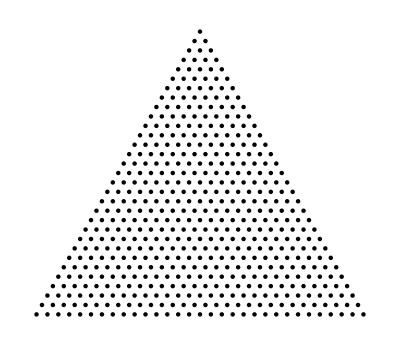

```mathematica
Graphics[{PointSize[.008],Point/@Select[rhombuspts,#[[1]]+(#[[2]])/(√3)<1&]}]
```

When I teach complex analysis, I always like to think about visualizations of the Riemann mapping theorem, which says we can conformally map any simply-connected open set in the plane to any other. So, given the above picture, a natural question to ask (at least for me) is: what does the above grid become if I conformally map the triangle to the disk?

Of course, the first sub-question is: what is an explicit conformal map from the triangle to the disk? In trying to figure this out, I stumbled across an answer Lukas Geyer gave on Math.StackExchange, which basically spells out how to find conformal transformations of certain triangles to the upper half-plane using elliptic functions. Then, given such a transformation, we can conformally map the upper half-plane to the unit disk using the Cayley transform:

```mathematica
Cayley[z_]:=(z-I)/(z+I);
```

In fact, the Wolfram Functions Site gives an explicit formula for the transformation we’re after in terms of ℘', the derivative of the Weierstrass ℘-function:

```mathematica
TriangleToDisk[z_]:=With[{e=N[WeierstrassPPrime[1,{0,(-Beta[1/3,1/3]^6)/729}]]},
I*Cayley[-1/(e √3)WeierstrassPPrime[z,{0,(-Beta[1/3,1/3]^6)/729}]]
];
```

The basic idea behind why elliptic functions pop up is that we can think of the equilateral triangle as half of a rhombus which is the fundamental domain of an elliptic function (that is, a doubly-periodic meromorphic function), and this gives a much easier way to back out a conformal map than the general Schwarz–Christoffel machinery.

So it makes some sense to grid out the full rhombus:

```mathematica
rhombuspts=With[{n=31},
N@Flatten[Table[ReIm[1/n(x+If[EvenQ[y],0,1/2]+I (√3)/2 y)],{y,0,n-1},{x,Floor[y/2],Floor[n+y/2]-1}],1]
];
```

If you feed the above triangular grid into TriangleToDisk, you get something like this:

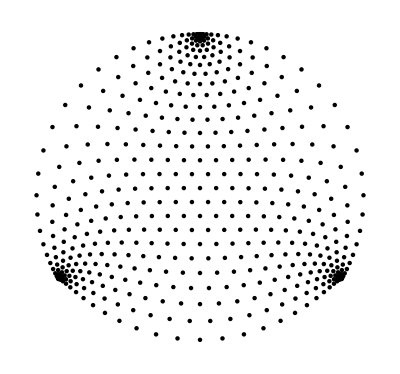

```mathematica
Module[{pts},
pts=ReIm[TriangleToDisk[Complex@@#]]&/@Select[rhombuspts,#[[1]]+(#[[2]])/(√3)<1&&Norm[#]>10^-12&];
Graphics[{PointSize[.008],Point/@pts},PlotRange->√2]
]
```

And if you feed the full rhombus in, you get this:

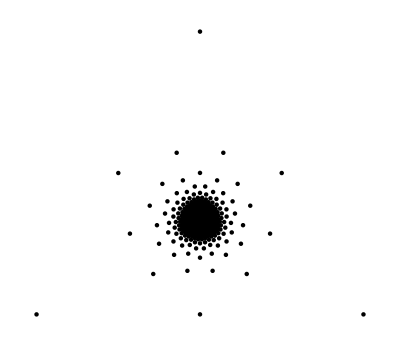

```mathematica
Module[{pts},
pts=ReIm[TriangleToDisk[Complex@@#]]&/@Select[rhombuspts,Norm[#]>10^-12&];
Graphics[{PointSize[.008],Point/@pts},PlotRange->√2]
]
```

Of course, this is a little bit misleading: if points are truly 0-dimensional, then a point is a point is a point, but when we visualize points we show a small disk. If we plug uniformly-sized disks into this transformation, we won’t get uniformly-sized disks out the other side. So, using CircleThrough, we can map disks to disks instead of just points to points:

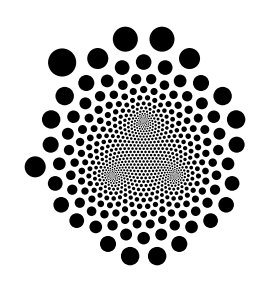

```mathematica
Module[{cols={Black, White},r=.011,pts},
Show[Graphics[{cols[[1]],Table[
pts=N@Table[ReIm[TriangleToDisk[Complex@@(rhombuspts[[tour[[2,i]]]])+r*p]],{p,{1,I,-1}}];
If[Norm[pts[[1]]]>3,Nothing,Disk@@CircleThrough[pts]],{i,1,Length[tour[[2]]]-1}]}],ImageSize->270,Background->cols[[2]],PlotRange->2]
]
```

That gives a much better sense of how this transformation is distorting area.

I spent a long time trying to figure out a nice way to animate this. In the end, I just decided to move the points around in some nice Hamiltonian Cycle. Specifically, I had Mathematica find an (approximate) solution to the Traveling Salesman Problem on the original points in the rhombus:

```mathematica
tour=FindShortestTour[rhombuspts];
```

Then we’ll just move the points along the tour and feed it all into TriangleToDisk. To make the transitions look a little nicer and more interesting, I use an easing function from Daniel Sanchez’s very nice repository function:

```mathematica
ease=ResourceFunction["EasingFunction"]["InOutElastic"];
```

Also, I inverted the colors for the final animation, which we build as a list of frames:

```mathematica
tri=Block[{cols={White,Black},r=.011,pts},
ParallelTable[Show[Graphics[{cols[[1]],Table[
pts=N@Table[ReIm[TriangleToDisk[Complex@@((1-ease[t])rhombuspts[[tour[[2,i]]]]+ease[t] rhombuspts[[tour[[2,i+1]]]])+r*p]],{p,{1,I,-1}}];
If[Norm[pts[[1]]]>3,Nothing,Disk@@CircleThrough[pts]],{i,1,Length[tour[[2]]]-1}]}],ImageSize->270,Background->cols[[2]],PlotRange->2],
{t,0.,1-#,#}]&[1/50.]
];
```

Which can then be exported as a GIF:

```mathematica
Export[NotebookDirectory[]<>"tri.gif",tri,"AnimationRepetitions"->Infinity,"DisplayDurations"->1/50];
```

Or viewed using ListAnimate:

```mathematica
ListAnimate[tri,50]
```